### Start choosing the example:

```mathematica
t=5;
beta=0;
A=0.2;
g[x]
```

Log[x]

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5},Adjacency Matrix→{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{5,U1}},Switching Costs→{}|>

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1-> 80, U1-> 15}]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

EliminateVarsSimplify for the us

Finished with the us!

Done!

{0.06169,<|u1→335,u2→255,u3→255,u4→175,u5→175,u6→95,u7→95,u8→15,u9→15,u10→15,u11→335,u12→335,j1→0,j2→80,j3→0,j4→80,j5→0,j6→80,j7→0,j8→80,j9→0,j10→80,j11→0,j12→80|>}

```mathematica
(rule=CriticalCongestionSolver2[d2e])//AbsoluteTiming
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

{0.004504,<|u1→335,u2→255,u3→255,u4→175,u5→175,u6→95,u7→95,u8→15,u9→15,u10→15,u11→335,u12→335,j1→0,j2→80,j3→0,j4→80,j5→0,j6→80,j7→0,j8→80,j9→0,j10→80,j11→0,j12→80|>}

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5},Adjacency Matrix→{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{5,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 2.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.011188,Null}

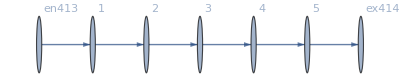

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j415→80.,j416→80.,j417→80.,j418→80.,j419→80.,j420→80.,j421→0.,j422→0.,j423→0.,j424→0.,j425→0.,j426→0.,jt427→0.,jt428→80.,jt429→80.,jt430→0.,jt431→80.,jt432→0.,jt433→80.,jt434→0.,jt435→80.,jt436→0.,u437→335.,u438→255.,u439→175.,u440→95.,u441→15.,u442→335.,u443→255.,u444→175.,u445→95.,u446→15.,u447→15.,u448→335.|>

#### Non-linear case

```mathematica
alpha=0;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

<|j415→80,j416→80,j417→80,j418→80,j419→80,j420→80,j421→0.,j422→0.,j423→0.,j424→0.,j425→0.,j426→0.,jt427→0.,jt428→80,jt429→80,jt430→0.,jt431→80,jt432→0.,jt433→80,jt434→0.,jt435→80,jt436→0.,u437→25.3278,u438→22.7459,u439→20.1639,u440→17.582,u441→15.,u442→25.3278,u443→22.7459,u444→20.1639,u445→17.582,u446→15.,u447→15.,u448→25.3278|>

```mathematica
alpha=0.1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

<|j415→80,j416→80,j417→80,j418→80,j419→80,j420→80,j421→0.,j422→0.,j423→0.,j424→0.,j425→0.,j426→0.,jt427→0.,jt428→80,jt429→80,jt430→0.,jt431→80,jt432→0.,jt433→80,jt434→0.,jt435→80,jt436→0.,u437→27.6454,u438→24.484,u439→21.3227,u440→18.1613,u441→15.,u442→27.6454,u443→24.484,u444→21.3227,u445→18.1613,u446→15.,u447→15.,u448→27.6454|>

```mathematica
alpha=0.3;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

<|j415→80,j416→80,j417→80,j418→80,j419→80,j420→80,j421→0.,j422→0.,j423→0.,j424→0.,j425→0.,j426→0.,jt427→0.,jt428→80,jt429→80,jt430→0.,jt431→80,jt432→0.,jt433→80,jt434→0.,jt435→80,jt436→0.,u437→35.0956,u438→30.0717,u439→25.0478,u440→20.0239,u441→15.,u442→35.0956,u443→30.0717,u444→25.0478,u445→20.0239,u446→15.,u447→15.,u448→35.0956|>

```mathematica
alpha=1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.7053×10^-13,ComplexInfinity]

<|j415→80,j416→80,j417→80,j418→80,j419→80,j420→80,j421→0.,j422→0.,j423→0.,j424→0.,j425→0.,j426→0.,jt427→0.,jt428→80,jt429→80,jt430→0.,jt431→80,jt432→0.,jt433→80,jt434→0.,jt435→80,jt436→0.,u437→335.,u438→255.,u439→175.,u440→95.,u441→15.,u442→335.,u443→255.,u444→175.,u445→95.,u446→15.,u447→15.,u448→335.|>

```mathematica
alpha=1.2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.00219×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.00219×10^-16

<|j415→80,j416→80,j417→80,j418→80,j419→80,j420→80,j421→0.,j422→0.,j423→0.,j424→0.,j425→0.,j426→0.,jt427→0.,jt428→80,jt429→80,jt430→0.,jt431→80,jt432→0.,jt433→80,jt434→0.,jt435→80,jt436→0.,u437→1470.62,u438→1106.72,u439→742.811,u440→378.906,u441→15.,u442→1470.62,u443→1106.72,u444→742.811,u445→378.906,u446→15.,u447→15.,u448→1470.62|>

```mathematica
alpha=1.6;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j415→80,j416→80,j417→80,j418→80,j419→80,j420→80,j421→0.,j422→0.,j423→0.,j424→0.,j425→0.,j426→0.,jt427→0.,jt428→80,jt429→80,jt430→0.,jt431→80,jt432→0.,jt433→80,jt434→0.,jt435→80,jt436→0.,u437→1.16019×10^6,u438→870144.,u439→580101.,u440→290058.,u441→15.,u442→1.16019×10^6,u443→870144.,u444→580101.,u445→290058.,u446→15.,u447→15.,u448→1.16019×10^6|>

```mathematica
alpha=1.7;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.38879×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.38879×10^-16

<|j415→80,j416→80,j417→80,j418→80,j419→80,j420→80,j421→0.,j422→0.,j423→0.,j424→0.,j425→0.,j426→0.,jt427→0.,jt428→80,jt429→80,jt430→0.,jt431→80,jt432→0.,jt433→80,jt434→0.,jt435→80,jt436→0.,u437→6.238×10^7,u438→4.6785×10^7,u439→3.119×10^7,u440→1.5595×10^7,u441→15.,u442→6.238×10^7,u443→4.6785×10^7,u444→3.119×10^7,u445→1.5595×10^7,u446→15.,u447→15.,u448→6.238×10^7|>

```mathematica
alpha=1.8;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.17196×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.17196×10^-16

<|j415→80,j416→80,j417→80,j418→80,j419→80,j420→80,j421→0.,j422→0.,j423→0.,j424→0.,j425→0.,j426→0.,jt427→0.,jt428→80,jt429→80,jt430→0.,jt431→80,jt432→0.,jt433→80,jt434→0.,jt435→80,jt436→0.,u437→9.62104×10^10,u438→7.21578×10^10,u439→4.81052×10^10,u440→2.40526×10^10,u441→15.,u442→9.62104×10^10,u443→7.21578×10^10,u444→4.81052×10^10,u445→2.40526×10^10,u446→15.,u447→15.,u448→9.62104×10^10|>

```mathematica
alpha=1.9;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.82736×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.82736×10^-16

<|j415→80,j416→80,j417→80,j418→80,j419→80,j420→80,j421→0.,j422→0.,j423→0.,j424→0.,j425→0.,j426→0.,jt427→0.,jt428→80,jt429→80,jt430→0.,jt431→80,jt432→0.,jt433→80,jt434→0.,jt435→80,jt436→0.,u437→2.24148×10^19,u438→1.68111×10^19,u439→1.12074×10^19,u440→5.6037×10^18,u441→15.,u442→2.24148×10^19,u443→1.68111×10^19,u444→1.12074×10^19,u445→5.6037×10^18,u446→15.,u447→15.,u448→2.24148×10^19|>

```mathematica
alpha=2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.84774×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.84774×10^-16

<|j415→80,j416→80,j417→80,j418→80,j419→80,j420→80,j421→0.,j422→0.,j423→0.,j424→0.,j425→0.,j426→0.,jt427→0.,jt428→80,jt429→80,jt430→0.,jt431→80,jt432→0.,jt433→80,jt434→0.,jt435→80,jt436→0.,u437→8.81959×10^106,u438→6.61469×10^106,u439→4.4098×10^106,u440→2.2049×10^106,u441→15.,u442→8.81959×10^106,u443→6.61469×10^106,u444→4.4098×10^106,u445→2.2049×10^106,u446→15.,u447→15.,u448→8.81959×10^106|>